# What is Chirality? How do we encounter it in our everyday, and not-so-everyday lives?

Cody Trevillian, Jun. 27, 2019

## I’m not sure, where do you see chirality in your daily life?

Look at your mirror-reflection:

```mathematica
ImageCapture[]
```

## Okay, easy! But...what does this have to do with chirality?

Everything! But, you have a point there. We can start simple and small. Have you ever seen a "rose chafer"?

```mathematica
{{-Graphics-, Dataset[<>]}}
```

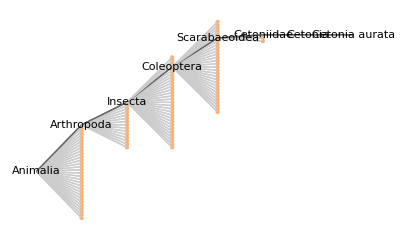
```mathematica
-Graphics-"(""nodes sorted by taxonomic diversity"")"
```

Well, maybe not if you live in the USA!

```mathematica
TextSentences[WikipediaData[Entity["Species","Species:CetoniaAurata"]]]⟦12;;13⟧
```

{Rose chafers are found in southern and central Europe and in the southern part of the United Kingdom, where they sometimes seem to be very localized.,They can also be found in South East Asia, in the countryside and outlying islands of Hong Kong.}

## This is all well and good, but why are we talking about a beetle?

Oh, right! So, check it out, the coloration of this awesome insect is chiral; the green-metallic coloration is due to a reflection of left-polarized light! Don’t believe me? Read it here:

```mathematica
TextSentences[WikipediaData[Entity["Species","Species:CetoniaAurata"]]]⟦23;;30⟧
```

{== Coloration ==,The metallic green coloration of the beetle is created structurally, caused by the reflection of mostly circularly polarised light;,like other scarabs this is left circularly polarised.,When viewed through a right circular polariser, the beetle appears to be colorless.,There are also different colors besides the common green;,there is also copper, grey and black.,A lot of specimens have white speckles while some have very few or none at all.,It has been described as a left-hand narrow-band elliptical polarizer.}

## Okay, I’m a little more lost than before, how does left-polarized light apply to chirality?

So, chirality is based on mirror-symmetry, if the mirror-reflection has no way of being reoriented through rotations and translations, then it is chiral, otherwise, it is achiral! This is just like the left- and right-handed polarizations of light that we see every day!

## I don’t quite understand, can you show me an example without light?

The following is a "trefoil", try rotating the left image to match it up with the right one:

```mathematica
{{-Graphics3D-, -Graphics-}}
```

So, you can see that this knot is chiral! Cool, huh?

## Okay...but I’ve never seen something like that before, can you give me a more...relatable example?

## Am “I” Chiral?

Well, no. “I”is not chiral, but “You” are!

```mathematica
{{-Graphics-}, {-Graphics-}}
```

## Alright, you made more art, but what does this mean to me?

Look at your hands. Make one look like the other, try it:

```mathematica
{{-Graphics3D-, -Graphics3D-}}
```

That’s chirality: Your hands are mirror-reflections of each other--you can’t superimpose one on the other, no matter how much you try!

## Wow! So, who discovered chirality? Louis Chiral?

Not quite! But close:

```mathematica
Entity["Person","LouisPasteur::d7488"]
```

```mathematica
{{-Graphics-, Dataset[<>]}}
```

It is surprising that the only contribution deemed worthy enough of Pasteur’s namesake were of his work on "pasteurization""  ""(""1864"")" !

## We are homo-chiral, exhibiting a uniformity of chirality: our proteins are exclusively left-handed, and our RNA and DNA are comprised of right-handed sugars. Let’s look at some chiral structures we enjoy every day in our lives:

### Try to reorient the left DNA strand like the right one, like the hands from before

```mathematica
{{-Graphics3D-, -Graphics-}}
```

Well, do you think you enjoy chirality?

## More than likely! Aren’t there some molecules like DNA that are the same, but not? Are those chiral?

Precisely! Now you’re getting it, check these out:

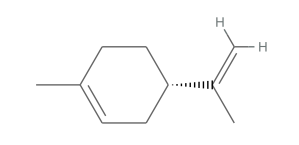
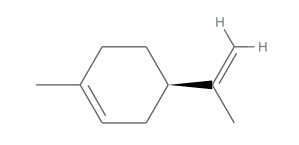
```mathematica
{{-Graphics3D-, -Graphics3D-}, {-Graphics-, -Graphics-}, {Entity["Chemical","SMinusLimonene"], Entity["Chemical","PlusLimonene"]}}{{-Graphics3D-, -Graphics3D-}, {-Graphics-, -Graphics-}, {Entity["Chemical","Levopropoxyphene"], Entity["Chemical","Dextropropoxyphene"]}}{{-Graphics3D-, -Graphics3D-}, {-Graphics-, -Graphics-}, {Entity["Chemical","RMinusCarvone"], Entity["Chemical","SPlusCarvone"]}}{{-Graphics3D-, -Graphics3D-}, {-Graphics-, -Graphics-}, {Entity["Chemical","DMinusTartaricAcid"], Entity["Chemical","LPlusTartaricAcid"]}}
```

Here, the (-) & (+), levo- & dextro-, (R)/(S) & (D)/(L) denote the chiral orientations of the molecules!

"D-tartaric acid" and "L-tartaric acid" are the molecules that "Louis Pasteur" first studied to observe chirality!  "(-)-limonene" comes from lemons, whereas "(+)-limonene" is found in oranges. "D-carvone" is from caraway seed oil, and "(R)-carvone" from spearmint oil. "levopropoxyphene" is known as Novrad and is an anti-cough agent, while "propoxyphene" is called Davron and is a painkiller.

You can see here that chirality is related to quite a great number of things:

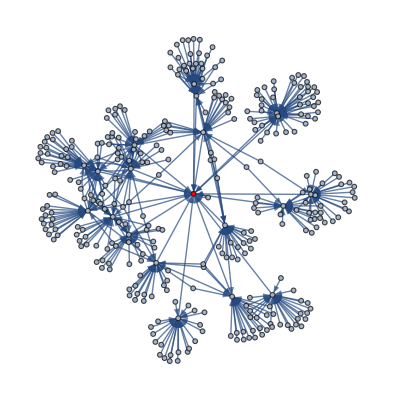

The coolest part about all of this, is that we can describe this mathematically. Give this a few glances:

## Hey! That looks like the DNA from up above, but it’s mathematical?

You’ve got that right! It is composed of the following, which can be descriptions of the mathematical functions that back left and right polarized light:

```mathematica
𝕩=Cos[# Pi/25]&/@Range@100;𝕩'=Cos[# Pi/25+Pi]&/@Range@100;
y=Cos[# Pi/25-Pi/2]&/@Range@100;y'=Cos[# Pi/25+Pi/2]&/@Range@100;
gchircos=Graphics3D[{{Thickness[0.03],Line[{#⟦1⟧,#⟦2⟧,#⟦3⟧}&/@ldatchircos]},
{Thickness[0.015],Green,Arrowheads[{0.015},Appearance->"Projected"],
Arrow[{1.5 #⟦1⟧,1.5 #⟦2⟧,#⟦3⟧}&/@ldatchircos⟦25;;75⟧]}},BoxRatios->{2,2,5},
AspectRatio->GoldenRatio,ImageSize->200,ViewAngle->Automatic,ViewCenter->{0.5,0.5,0.5},
ViewMatrix->Automatic,ViewPoint->{1.4000620728320412,0.013476838199693643,3.0805266704005962},
ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,
ViewVertical->{-0.8145880655494367,-0.004512056440937054,0.5800223485445198}];
gcos=Graphics3D[{{Thickness[0.03],Line[{#⟦1⟧,#⟦2⟧,#⟦3⟧}&/@ldatcos]},
{Thickness[0.015],Green,Arrowheads[{0.015},Appearance->"Projected"],
Arrow[{1.5 #⟦1⟧,1.5 #⟦2⟧,#⟦3⟧}&/@ldatcos⟦25;;75⟧]}},BoxRatios->{2,2,5},
AspectRatio->GoldenRatio,ImageSize->200,ViewAngle->Automatic,ViewCenter->{0.5,0.5,0.5},
ViewMatrix->Automatic,ViewPoint->{1.4000620728320412,0.013476838199693643,3.0805266704005962},
ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,
ViewVertical->{-0.8145880655494367,-0.004512056440937054,0.5800223485445198}];
Show[{g,gchir}]
```

## Wow. It all comes together, how amazing!

Yup! Thanks for chatting with me about Chirality!!

## Of course, and thank you for letting me in on such a beautiful secret that surrounds all of us!

Any time. Here’s one last fun example to take home with you:

```mathematica
{{-Graphics-, -Graphics-}}
```